## Singular Value Decomposition (SVD)

### Pictures

#### Pictures: ℝ^(2×2)

For any A∈ℝ^(2×2) the image of the unit circle is an ellipse!  The directions and lengths of the axes are clearly of interest!

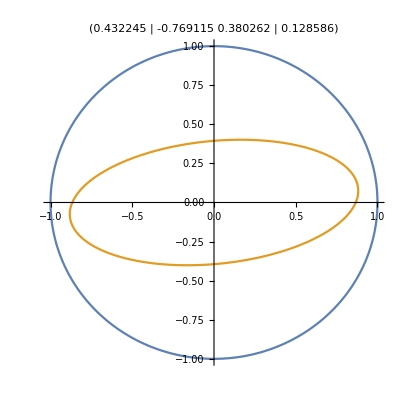

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];
ParametricPlot[{{Cos[θ],Sin[θ]},A.{Cos[θ],Sin[θ]}},{θ,0,2π},PlotRange->All,
PlotLabel->A]
```

#### Pictures: ℝ^(3×3)

For any A∈ℝ^(3×3) the image of the unit sphere is an ellipsoid!  The directions and lengths of the axes are clearly of interest!

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];
ParametricPlot3D[{
{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]},
A.{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]}
},{θ,0,2π},{ϕ,0,π},PlotRange->All,
Mesh->All]
```

-Graphics3D-

#### Pictures: ℝ^(3×2)

For any A∈ℝ^(3×2) the image of the unit circle is an ellipse in 3D!  The directions and lengths of the axes are clearly of interest!

```mathematica
{m,n}={3,2};
A=RandomReal[{-1,1},{m,n}];
ParametricPlot3D[{
A.{Cos[θ],Sin[θ]}
},{θ,0,2π},PlotRange->All,
PlotLabel->A]
```

-Graphics3D-

#### Pictures: ℝ^(2×3)

For any A∈ℝ^(2×3) the image of the unit sphere is an ellipse!  The directions and lengths of the axes are clearly of interest!  The ellipse is covered more than once but it is an ellipse.

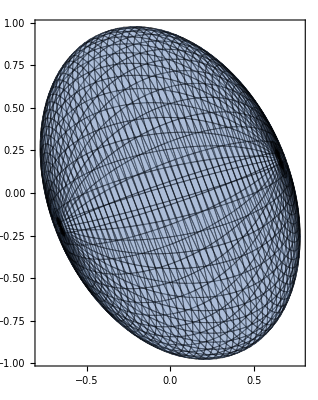

```mathematica
{m,n}={2,3};
A=RandomReal[{-1,1},{m,n}];

ParametricPlot[{
A.{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]}
},{θ,0,2π},{ϕ,0,π},PlotRange->All,
Mesh->All]
```

### SVD: Geometric Interpretation

#### SVD: ℝ^(2×2)

The SVD gives us the axes directions and lengths. The column vectors in U are the directions of the axes and the diagonal entries of the diagonal matrix S are the matching lengths.

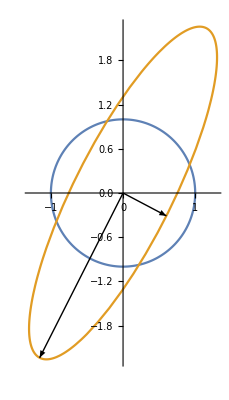

```mathematica
m=2;A=RandomReal[{-2,2},{m,m}];
{U,S,V}=SingularValueDecomposition[A];
{u1,u2}=Uᵀ;{σ1,σ2}=Diagonal[S];
ParametricPlot[{{Cos[θ],Sin[θ]},A.{Cos[θ],Sin[θ]}},{θ,0,2π},PlotRange->All,
Epilog->{{Arrow[{{0,0},σ1 u1}], Arrow[{{0,0},σ2 u2}]}}
]
```

#### SVD: ℝ^(3×3)

The SVD gives us the axes directions and lengths. The column vectors in U are the directions of the axes and the diagonal entries of the diagonal matrix S are the matching lengths.

```mathematica
m=3;A=RandomReal[{-1,1},{m,m}];
{U,S,V}=SingularValueDecomposition[A];
{u1,u2,u3}=Uᵀ;{σ1,σ2,σ3}=Diagonal[S];
Show[
ParametricPlot3D[A.{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]},
{θ,0,2π},{ϕ,0,π},PlotRange->All,
PlotStyle->Opacity[0.2]
],
Graphics3D[{Red,Arrow[{{0,0,0},σ1 u1}], 
Arrow[{{0,0,0},σ2 u2}],
Arrow[{{0,0,0},σ3 u3}]}]]
```

-Graphics3D-

#### SVD: ℝ^(3×2)

For any A∈ℝ^(3×2) the image of the unit circle is an ellipse in 3D!  The SVD gives the info

```mathematica
{m,n}={3,2};A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
{u1,u2,u3}=Uᵀ;
{σ1,σ2}=Diagonal[S];
Show[
ParametricPlot3D[{
A.{Cos[θ],Sin[θ]}
},{θ,0,2π},PlotRange->All],
Graphics3D[{Red,Arrow[{{0,0,0},σ1 u1}], 
Arrow[{{0,0,0},σ2 u2}],
Green,Arrow[{{0,0,0},u3}]}]]
```

-Graphics3D-

#### SVD: ℝ^(2×3)

For any A∈ℝ^(2×3) the image of the unit sphere is an ellipse!  The directions and lengths of the axes are clearly of interest!  The ellipse is covered more than once but it is an ellipse.

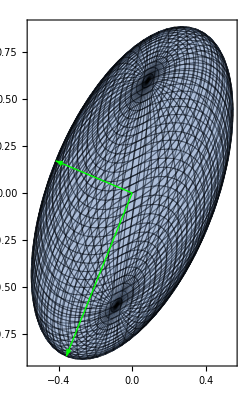

```mathematica
{m,n}={2,3};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
{u1,u2}=Uᵀ;
{σ1,σ2}=Diagonal[S];
ParametricPlot[{
A.{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]}
},{θ,0,2π},{ϕ,0,π},PlotRange->All,
Mesh->All,
Epilog->{Green,Arrow[{{0,0},σ1 u1}],Arrow[{{0,0},σ2 u2}]}
]
```

### SVD: Algebraic Interpretation

I do not know how to draw pictures in general dimensions!

Algebraically the SVD of A∈ℝ^(m×n) gives 
	A=U.S.Vᵀ
where the columns u_k of the m×m matrix U form an orthogonal basis for the output space ℝ^m and the diagonal of the m×n diagonal matrix S gives axis lengths σ_k of the output m-dimensional hyper-ellipse.  The columns of the n×n orthogonal matrix V  give the input vectors v_k that match u_k in the sense that 
	σ_k u_k=A.v_k
The singular values σ_k (the non-negative diagonals of S) are ordered
	σ_1≥σ_2≥…

```mathematica
{m,n}={4,5};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
Map[Norm,{A-U.S.Vᵀ,Uᵀ.U-IdentityMatrix[m],Vᵀ.V-IdentityMatrix[n]}]
MatrixForm[S]
```

{1.45073×10^-15,5.09344×10^-16,6.33628×10^-16}

(2.0946 | 0. | 0. | 0. | 0.
0. | 1.39557 | 0. | 0. | 0.
0. | 0. | 0.54752 | 0. | 0.
0. | 0. | 0. | 0.439901 | 0.)

{{-0.694838,-0.0185977,-0.0256047,-0.649886,-0.856066,0.201534,-0.414387,-0.0241107,0.640113,0.472892,-0.481338,0.948007},{0.940384,0.0645557,-0.958914,0.331323,0.454862,0.718985,-0.30713,0.676787,-0.945421,-0.333297,0.688814,-0.485074}}

{4.21286}

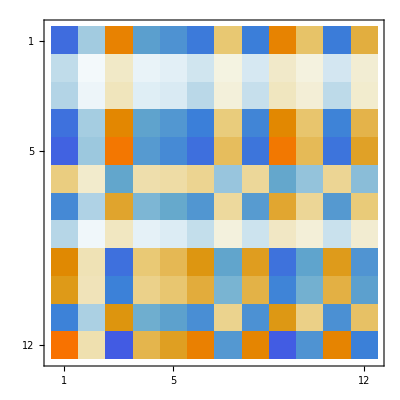

```mathematica
m=12;
{u,v}=RandomReal[{-1,1},{2,m}]
uv = KroneckerProduct[u,v];
SingularValueList[uv]
MatrixPlot[uv]
```

### SVD: Thick vs Thin aka Full vs Reduced

A thin SVD drops zero rows and/or columns from the center scaling matrix S and drops the corresponding columns from U and V. In practice, you frequently tell software how many singular values you want (say r) and the software gives you the pieces matching the r biggest singular values!  You now have A≈U.S.Vᵀ but now U and V  are Tall-Skinny matrices. Of course, the columns of U and V are still orthogonal. 

Caution: By default some software gives thin SVDs while some gives thick SVDs.

Mathematica and matlab give thick SVDs by default.  Julia gives a thin svd by default.

```mathematica
{m,n,r}={10,12,5}
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A,r];
Map[Dimensions,{A,U,S,V}]
Map[Norm,{Uᵀ.U-IdentityMatrix[r],Vᵀ.V-IdentityMatrix[r]}]
{Norm[Diagonal[S]],Norm[A,"Frobenius"]}
```

{10,12,5}

{{10,12},{10,5},{5,5},{12,5}}

{6.94754×10^-16,1.26472×10^-15}

{5.74222,6.11862}

### Rotationally Invariant Matrix Norms from SVD: A=U.S.Vᵀ

If ||A||=||Q_1.A.Q_2|| for all rotations then 
	||A||=||U.S.Vᵀ||=||Uᵀ.U.S.Vᵀ.V||=||S||
So if σ_r>0 and σ_(r+1)=0 then r is the rank of A and 
	||A(||)_F^2=∑_(i=1)^r σ_i^2
and ||A(||)_2=σ_1. Any rotationally invariant matrix norm is determined by the singular values.  There are Schatten and Ky-Fan norms (this is what I would call a Schatten “p” Ky-Fan “k” norm)
	||σ⟦1;;k⟧(||)_p=(∑_(i=1)^k σ_i^p)^(1/p).
These are sufficiently unusual that they do not have a standard notation.  One special case (the Nuclear Norm) does
	||A(||)_*=∑_(i=1)^r σ_i
It is widely used as a proxy for rank!

## SVD: Interpretation

We can pretend any matrix is diagonal!  All we have to do is use the correct basis for the input and output spaces.

The thick SVD gives us complete information on the matrix!

The rank r of A is the number of non-zero singular values.

The range of A is the span of u_1,u_2,…,u_r and the null space of A is the span of v_(r+1),v_(r+2),…,v_n

||A(||)_2=σ_1 and ||A(||)_F^2=σ_1^2+σ_2^2+…+σ_r^2

The non-zero singular values of A are the square roots of the non-zero eigenvalues of A^*.A or A.A^*

If A=A^* then singular values are the absolute values of the eigenvalues.

```mathematica
{m,n,r}={14,10,3};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A,r];
Map[Dimensions,{A,U,S,V}]
Map[Norm,{Uᵀ.U-IdentityMatrix[r],Vᵀ.V-IdentityMatrix[r]}]
```

{{14,10},{14,3},{3,3},{10,3}}

{1.28552×10^-15,2.23463×10^-15}

### Singular Value Spectra of Real World Matrices

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/SPARSKIT/drivcav_old/cavity08.mtx.gz"]
{m,n}=Dimensions[A]
σs=SingularValueList[A];
TruncatedNorms=Table[Norm[σs⟦1;;i⟧],{i, 1, Min[m,n]}];
PercentNorms=100TruncatedNorms/Norm[A,"Frobenius"];
TabView[{
"σs"->ListLogPlot[σs,PlotRange->All,GridLines->Automatic],
"Norms"->ListPlot[TruncatedNorms,PlotRange->All,GridLines->Automatic],
"%"->ListLogLogPlot[PercentNorms,PlotRange->All,GridLines->Automatic]
}]
```

SparseArray[…]

{1182,1182}

SingularValueList::arh: Because finding 1182 out of the 1182 singular values and/or singular vectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer singular values and/or singular vectors would be sufficient, consider restricting this number using the second argument to SingularValueList.

123

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/econaus/mahindas.mtx.gz"]
{m,n}=Dimensions[A]
σs=SingularValueList[A];
TruncatedNorms=Table[Norm[σs⟦1;;i⟧],{i, 1, Min[m,n]}];
PercentNorms=100TruncatedNorms/Norm[A,"Frobenius"];
TabView[{
"σs"->ListLogPlot[σs,PlotRange->All,GridLines->Automatic],
"Norms"->ListPlot[TruncatedNorms,PlotRange->All,GridLines->Automatic],
"%"->ListLogLogPlot[PercentNorms,PlotRange->All,GridLines->Automatic]
}]
```

SparseArray[…]

{1258,1258}

SingularValueList::arh: Because finding 1258 out of the 1258 singular values and/or singular vectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer singular values and/or singular vectors would be sufficient, consider restricting this number using the second argument to SingularValueList.

123

### SVD: Optimal Low Rank Approximation

A thin SVD for a rank r matrix A gives a low rank approximation for A
	A≈A_(μ)=∑_(k=1)^μ σ_k u_k⊗v_k=∑_(k=1)^μ σ_k u_k.v_k^*
In fact, A_(μ) is the best low rank approximation in two senses
	A_(μ) | = | argmin_(rank(B)≤μ) ||A-B(||)_2
A_(μ) | = | argmin_(rank(B)≤μ) ||A-B(||)_F
with ||A-A_(μ)(||)_2=σ_(μ+1) and ||A-A_(μ)(||)_F^2=∑_(k=μ+1)^r σ_k^2.

The proof is easy! Since both norms are unchanged by left or right multiplication by unitary matrices. We can consider the diagonal matrix S=Uᵀ.A.V where A=U.S.Vᵀ is the SVD of A.  The result is pretty clear for diagonal matrices with ordered diagonals.

### SVD: Decomposition and Synthesis

```mathematica
{m,n,r}={12,8,3};
R= RandomReal[{-1,1},{m,r}];
T= RandomReal[{-1,1},{n,r}];
W= RandomReal[{-1,1},{r,r}];
A=R.W.Tᵀ;
{UF,SF,VF}=SingularValueDecomposition[A];
{UR,SR,VR}=SingularValueDecomposition[A,r];
MatrixForm[SR]
MatrixForm[SF]
```

(5.83711 | 0. | 0.
0. | 1.59425 | 0.
0. | 0. | 0.194342)

(5.83711 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.59425 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.194342 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

### Eigenvalue Decomposition (EVD) and Synthesis

Everyone should know that eigenvalues λ and eigenvectors v satisfy 
	A v = λ v.
Most (but not all) square matrices A∈ℂ^(m×m) have a complete set of m linearly independent eigenvectors which can be  assembled columns  X=(v_1 | | | v_2 | | | … | | | v_m) satisfying A=X.Λ.X^-1 where Λ is the diagonal matrix with the eigenvalues on the diagonal.

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];
{λ,X}=Eigensystem[A];X=Xᵀ;
Norm[A-X.DiagonalMatrix[λ].Inverse[X]]
```

1.73099×10^-14

If A is Hermitian A=A^*=OverBar[(Aᵀ)] then you can chose a unitary eigenvector matrix U i.e. 
	A=U.Λ.U^*
If A is real symmetric A=Aᵀ then everything is real and you can chose an orthogonal eigenvector matrix Q i.e. 
	A=Q.Λ.U^ᵀ

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
{λ,Q}=Eigensystem[A];Q=Qᵀ;
Norm[A-Q.DiagonalMatrix[λ].Qᵀ]
```

1.20873×10^-14

You can make matrices with specifc eigenvalues!

```mathematica
λ={1,2,7};
m=Length[λ];
Q=Orthogonalize[RandomReal[{-1,1},{m,m}]];
MatrixForm[A=Q.DiagonalMatrix[λ].Qᵀ]
Eigenvalues[A]
```

(3.30423 | 0.923569 | -2.34886
0.923569 | 2.63635 | -1.85911
-2.34886 | -1.85911 | 4.05942)

{7.,2.,1.}

## SVD vs (Eigen Value Decomposition)EVD

Existence

Every rectangular or square matrix has an SVD A=U Σ Vᵀ

Most square matrices have an EVD A=X Λ X^-1

Real vs Complex

A real matrix has a real SVD A=U Σ Vᵀ

Most non-symmetric A≠Aᵀ real matrices have complex eigenvalues and eigenvectors.

The second half of our course is going to be about computing SVDs and EVDs.